```mathematica
(*This notebook will show plots of the physical patch model. Here only one patch will be considered. The angle which the patch on particle i makes around the y-axis is α, angle of the patch on particle j around y-axis is θ, and the angle around the z-axis of particle j is called ϕ. The particle particle distance, R, will be be aligned along the z-axis, pi and pj are the patch vectors of partice i and j respectively. thetai is defined as the angle between patch vector pi and the vector connecting pj and ri. thetaj is defined as the angle between patch vector pj and the vector connecting pi and rj*)
```

```mathematica
pi[alpha_]:={Sin[alpha*π/180.],0,Cos[alpha*π/180.]}
pj[theta_,phi_]:= {Sin[theta*π/180.]*Cos[phi*π/180.],Sin[theta*π/180.]*Sin[phi*π/180.],-Cos[theta*π/180.]}

ri:={0,0,0}
rj[R_]:={0,0,R}

ui[alpha_]:=0.5*pi[alpha]+ri
uj[theta_,phi_,R_]:=0.5*pj[theta,phi]+rj[R]

rij[R_]:= Norm[ri-rj[R]]
uij[alpha_,theta_,phi_,R_]:=Norm[ui[alpha]-uj[theta,phi,R]]

sigmatilde[sigma_]:=((2^(1/6)-sigma)/2^(1/6))*sigma

Vrep[R_,sig_]:=4((sigmatilde[sig]/(R-sig))^12-(sigmatilde[sig]/(R-sig))^6 +0.25 )HeavisideTheta[2^(1/6)-R]
Vatt[R_,epsP_,sig_]:= -epsP(sig/R)^6


PotOnePatch[alpha_,theta_,phi_,R_,sigR_,sigP_,epsP_]:=Vrep[R,sigR]+Vatt[uij[alpha,theta,phi,R],epsP,sigP]
```

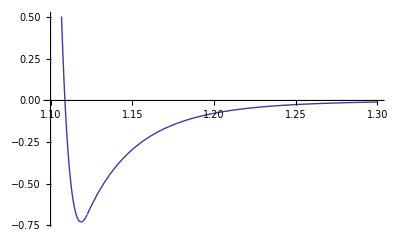

```mathematica
epsP=10;
Plot[PotOnePatch[0,10,0,R,1.0,0.1,epsP],{R,1.1,1.3},PlotLegends->Automatic,PlotRange->Automatic]
```

```mathematica
ContourPlot[PotOnePatch[alpha,0,0,R,1.0,0.1,1.0],{alpha,-90,90},{R,1.1,1.3},PlotLegends->Automatic,Contours->10,PlotRange->All]
```

-Graphics-